```mathematica
Needs["NVSim`"]
```

### Overview

The main function of NVSim is EvalPulse[H,p], where H is the Hamiltonian, and p is the pulse. By pulse, we mean one of three things:

(1)  A drift pulse: the evolution under the Hamiltonian for some time. In this case, p is just equal to a number, or a Symbol such as “t”.

(2)  An instantaneous pulse: the Hamiltonian is ignored and some other unitary is applied. This kind of pulse only really makes within pulse sequences. In this case, p is of the form {U,t} where U is the unitary matrix and t is how much time the pulse should take.

(3)   A shaped pulse: A list of control Hamiltonians, time spacings, and amplitudes is provided, and everything is simulated. In this case, p is of the form {pulse,{Hctl1,Hctl2,...}} where pulse is either a text file (eg. CVS) containing the pulse, or the pulse itself. A pulse is of the form {dt1,a11,a12,a13,...},{dt2,a21,a22,a23,...},{dt2,a21,a22,a23,...},...}.

The Hamiltonian H can be either time dependent, in which case it is just a matrix, or time dependent, in which case it is a function taking one real argument, and returning a matrix. For example:

```mathematica
TimeDepHam=3Z;
TimeIndepHam[t_]=Cos[t]Z;
```

In addition to the inputs H and p, there are also several options. Instead of explicitly listing them all and what they do, for this would be tedious, I will trust that you can garner their meanings from the examples which follow. I will mention, however, that you can view all the options by typing:

```mathematica
Options[SimulationOptions]
```

{StepSize→Automatic,PollingInterval→Off,InitialState→None,Observables→None,Functions→None,SimulationOutput→Automatic,SequenceMode→False,NumericEvaluation→True}

And moreover, that using the ? symbol will yeild quick descriptions:

```mathematica
?StepSize
```

StepSize is a simulation option that chooses the time discretization when the internal Hamiltonian is time dependent. Can be set to Automatic.

### Simplest Example

We evolve under X/2 for a time π:

```mathematica
EvalPulse[X/2,π]//Chop
```

{{Unitaries,{{{1,0},{0,1}},{{0,0.-1. ⅈ},{0.-1. ⅈ,0}}}},{TimeVector,{0,π}}}

The TimeVector shows the times at which an output is returned. Since we have not entered an initial state, the output defaults to displaying the unitaries at these times. In this simple example we see that at time 0, we have the identity unitary, and at time π, we have e^(-I π X/2).

### Next Simplest Examples: Using Options

#### InitialState

If we enter an initial state, the output automatically chooses to track this state over time:

```mathematica
ρ0={{1,0},{0,0}};
EvalPulse[X/2,π,InitialState->ρ0]//Chop
```

{{States,{{{1,0},{0,0}},{{0,0},{0,1.}}}},{TimeVector,{0,π}}}

Now we know the state of the system at all times in the TimeVector.

#### PollingInterval

We may want to know things about the system at intermedate times. This is done through PollingInterval.

```mathematica
ρ0={{1,0},{0,0}};
EvalPulse[X/2,π,InitialState->ρ0,PollingInterval->0.3]
```

{{States,{{{1,0},{0,0}},{{0.979746+0. ⅈ,0.+0.140866 ⅈ},{0.-0.140866 ⅈ,0.0202535+0. ⅈ}},{{0.920627+0. ⅈ,0.+0.27032 ⅈ},{0.-0.27032 ⅈ,0.0793732+0. ⅈ}},{{0.82743+0. ⅈ,0.+0.377875 ⅈ},{0.-0.377875 ⅈ,0.17257+0. ⅈ}},{{0.707708+0. ⅈ,0.+0.454816 ⅈ},{0.-0.454816 ⅈ,0.292292+0. ⅈ}},{{0.571157+0. ⅈ,0.+0.494911 ⅈ},{0.-0.494911 ⅈ,0.428843+0. ⅈ}},{{0.428843+0. ⅈ,0.+0.494911 ⅈ},{0.-0.494911 ⅈ,0.571157+0. ⅈ}},{{0.292292+0. ⅈ,0.+0.454816 ⅈ},{0.-0.454816 ⅈ,0.707708+0. ⅈ}},{{0.17257+0. ⅈ,0.+0.377875 ⅈ},{0.-0.377875 ⅈ,0.82743+0. ⅈ}},{{0.0793732+0. ⅈ,0.+0.27032 ⅈ},{0.-0.27032 ⅈ,0.920627+0. ⅈ}},{{0.0202535+0. ⅈ,0.+0.140866 ⅈ},{0.-0.140866 ⅈ,0.979746+0. ⅈ}},{{6.93335×10^-33+0. ⅈ,0.+8.32667×10^-17 ⅈ},{0.-8.32667×10^-17 ⅈ,1.+0. ⅈ}}}},{TimeVector,{0,π/11,(2 π)/11,(3 π)/11,(4 π)/11,(5 π)/11,(6 π)/11,(7 π)/11,(8 π)/11,(9 π)/11,(10 π)/11,π}}}

Now we know the state of the system every 0.3 units of time. Notice that PollingInterval does not have to evenly divide the total evolution time. This is in general true, PollingInterval need have no relation to any time scale in your problem.

#### Observables

You may want to track the expectation values of some observables. This can be done through Observables:

```mathematica
ρ0={{1,0},{0,0}};
EvalPulse[X/2,π,InitialState->ρ0,PollingInterval->0.3,Observables->{Z}]
```

{{Observables,{{1},{0.959493},{0.841254},{0.654861},{0.415415},{0.142315},{-0.142315},{-0.415415},{-0.654861},{-0.841254},{-0.959493},{-1.}}},{TimeVector,{0,π/11,(2 π)/11,(3 π)/11,(4 π)/11,(5 π)/11,(6 π)/11,(7 π)/11,(8 π)/11,(9 π)/11,(10 π)/11,π}}}

Note that Observables must be a list even if we are only interested in only one observable. We can also track multiple observables:

```mathematica
ρ0={{1,0},{0,0}};
EvalPulse[X/2,π,InitialState->ρ0,PollingInterval->0.3,Observables->{X,Y,Z}]
```

{{Observables,{{0,0,1},{0.,-0.281733,0.959493},{0.,-0.540641,0.841254},{0.,-0.75575,0.654861},{0.,-0.909632,0.415415},{0.,-0.989821,0.142315},{0.,-0.989821,-0.142315},{0.,-0.909632,-0.415415},{0.,-0.75575,-0.654861},{0.,-0.540641,-0.841254},{0.,-0.281733,-0.959493},{0.,-1.66533×10^-16,-1.}}},{TimeVector,{0,π/11,(2 π)/11,(3 π)/11,(4 π)/11,(5 π)/11,(6 π)/11,(7 π)/11,(8 π)/11,(9 π)/11,(10 π)/11,π}}}

#### Functions

You may want to track the evolution of some arbitrary function(s), like the purity of a subsystem. This can be done through Functions, which is similar in flavour to Observables.

```mathematica
ρ0=Projector[{0,1,0,0}];
f[ρ_]:=Purity[PartialTr[ρ,{2,2},{2}]];
EvalPulse[𝟙⊗Z+Z⊗𝟙+X⊗X+Y⊗Y+Z⊗Z,10π,PollingInterval->1,InitialState->ρ0,Functions->{f}]//Chop
```

{{Functions,{{1},{0.75},{0.5},{0.75},{1.},{0.75},{0.5},{0.75},{1.},{0.75},{0.5},{0.75},{1.},{0.75},{0.5},{0.75},{1.},{0.75},{0.5},{0.75},{1.},{0.75},{0.5},{0.75},{1.},{0.75},{0.5},{0.75},{1.},{0.75},{0.5},{0.75},{1.}}},{TimeVector,{0,(5 π)/16,(5 π)/8,(15 π)/16,(5 π)/4,(25 π)/16,(15 π)/8,(35 π)/16,(5 π)/2,(45 π)/16,(25 π)/8,(55 π)/16,(15 π)/4,(65 π)/16,(35 π)/8,(75 π)/16,5 π,(85 π)/16,(45 π)/8,(95 π)/16,(25 π)/4,(105 π)/16,(55 π)/8,(115 π)/16,(15 π)/2,(125 π)/16,(65 π)/8,(135 π)/16,(35 π)/4,(145 π)/16,(75 π)/8,(155 π)/16,10 π}}}

Next we ask for both some observables and functions:

```mathematica
ρ0=Projector[{0,1,0,0}];
f[ρ_]:=Purity[PartialTr[ρ,{2,2},{2}]];
EvalPulse[𝟙⊗Z+Z⊗𝟙+X⊗X+Y⊗Y+Z⊗Z,10π,PollingInterval->1,InitialState->ρ0,Functions->{f},Observables->{Z⊗𝟙}]//Chop
```

{{Observables,{{1},{-0.707107},{0},{0.707107},{-1.},{0.707107},{0},{-0.707107},{1.},{-0.707107},{0},{0.707107},{-1.},{0.707107},{0},{-0.707107},{1.},{-0.707107},{0},{0.707107},{-1.},{0.707107},{0},{-0.707107},{1.},{-0.707107},{0},{0.707107},{-1.},{0.707107},{0},{-0.707107},{1.}}},{Functions,{{1},{0.75},{0.5},{0.75},{1.},{0.75},{0.5},{0.75},{1.},{0.75},{0.5},{0.75},{1.},{0.75},{0.5},{0.75},{1.},{0.75},{0.5},{0.75},{1.},{0.75},{0.5},{0.75},{1.},{0.75},{0.5},{0.75},{1.},{0.75},{0.5},{0.75},{1.}}},{TimeVector,{0,(5 π)/16,(5 π)/8,(15 π)/16,(5 π)/4,(25 π)/16,(15 π)/8,(35 π)/16,(5 π)/2,(45 π)/16,(25 π)/8,(55 π)/16,(15 π)/4,(65 π)/16,(35 π)/8,(75 π)/16,5 π,(85 π)/16,(45 π)/8,(95 π)/16,(25 π)/4,(105 π)/16,(55 π)/8,(115 π)/16,(15 π)/2,(125 π)/16,(65 π)/8,(135 π)/16,(35 π)/4,(145 π)/16,(75 π)/8,(155 π)/16,10 π}}}

Functions do not have to return numbers; they can return anything you want. For example you can return subsystems:

```mathematica
f[ρ_]:=PartialTr[ρ,{2,2},{1}]
```

#### Customizing the output

You may have noticed that the output of the EvalPulse was chosen automatically for you in the previous examples. Suppose that you want something other than what it’s giving you, e.g. you want both the States and the Observables. You can use SimulationOutput to acheive this.

```mathematica
ρ0={{1,0},{0,0}};
EvalPulse[X/2,π,InitialState->ρ0,PollingInterval->0.3,Observables->{Z},SimulationOutput->{States,Observables}]
```

{{States,{{{1,0},{0,0}},{{0.979746+0. ⅈ,0.+0.140866 ⅈ},{0.-0.140866 ⅈ,0.0202535+0. ⅈ}},{{0.920627+0. ⅈ,0.+0.27032 ⅈ},{0.-0.27032 ⅈ,0.0793732+0. ⅈ}},{{0.82743+0. ⅈ,0.+0.377875 ⅈ},{0.-0.377875 ⅈ,0.17257+0. ⅈ}},{{0.707708+0. ⅈ,0.+0.454816 ⅈ},{0.-0.454816 ⅈ,0.292292+0. ⅈ}},{{0.571157+0. ⅈ,0.+0.494911 ⅈ},{0.-0.494911 ⅈ,0.428843+0. ⅈ}},{{0.428843+0. ⅈ,0.+0.494911 ⅈ},{0.-0.494911 ⅈ,0.571157+0. ⅈ}},{{0.292292+0. ⅈ,0.+0.454816 ⅈ},{0.-0.454816 ⅈ,0.707708+0. ⅈ}},{{0.17257+0. ⅈ,0.+0.377875 ⅈ},{0.-0.377875 ⅈ,0.82743+0. ⅈ}},{{0.0793732+0. ⅈ,0.+0.27032 ⅈ},{0.-0.27032 ⅈ,0.920627+0. ⅈ}},{{0.0202535+0. ⅈ,0.+0.140866 ⅈ},{0.-0.140866 ⅈ,0.979746+0. ⅈ}},{{6.93335×10^-33+0. ⅈ,0.+8.32667×10^-17 ⅈ},{0.-8.32667×10^-17 ⅈ,1.+0. ⅈ}}}},{Observables,{{1},{0.959493},{0.841254},{0.654861},{0.415415},{0.142315},{-0.142315},{-0.415415},{-0.654861},{-0.841254},{-0.959493},{-1.}}},{TimeVector,{0,π/11,(2 π)/11,(3 π)/11,(4 π)/11,(5 π)/11,(6 π)/11,(7 π)/11,(8 π)/11,(9 π)/11,(10 π)/11,π}}}

#### NumericEvaluation

By default in NVSim, times are turned into floating point numbers right before they are put into the matrix exponential (e.g. MatrixExp[-I N[t] H]):

```mathematica
EvalPulse[X/2,π/2]
```

{{Unitaries,{{{1,0},{0,1}},{{0.707107+0. ⅈ,0.-0.707107 ⅈ},{0.-0.707107 ⅈ,0.707107+0. ⅈ}}}},{TimeVector,{0,π/2}}}

This can be circumvented with the NumericEvaluation option:

```mathematica
EvalPulse[X/2,π/2,NumericEvaluation->False]
```

{{Unitaries,{{{1,0},{0,1}},{{1/(√2),-ⅈ/(√2)},{-ⅈ/(√2),1/(√2)}}}},{TimeVector,{0,π/2}}}

### Methods for formatting the output with applications toward plotting

The functions TimeVector, Unitaries, States, Observables, and Functions, in addition to serving as placeholders as seen in the previous section, can be used to format the output.

#### TimeVector

TimeVector simply extracts the TimeVector:

```mathematica
ρ0={{1,0},{0,0}};
data=EvalPulse[X/2,π]
TimeVector[data]
```

{{Unitaries,{{{1,0},{0,1}},{{1.50134×10^-16+0. ⅈ,0.-1. ⅈ},{0.-1. ⅈ,1.50134×10^-16+0. ⅈ}}}},{TimeVector,{0,π}}}

{0,π}

#### Unitaries

Unitaries simply extracts the Unitaries:

```mathematica
data=EvalPulse[X/2,π]
Unitaries[data]
```

{{Unitaries,{{{1,0},{0,1}},{{1.50134×10^-16+0. ⅈ,0.-1. ⅈ},{0.-1. ⅈ,1.50134×10^-16+0. ⅈ}}}},{TimeVector,{0,π}}}

{{{1,0},{0,1}},{{1.50134×10^-16+0. ⅈ,0.-1. ⅈ},{0.-1. ⅈ,1.50134×10^-16+0. ⅈ}}}

Unitaries[data,t] extracts the unitary from the list Unitaries[data] whose time lies closest to t:

```mathematica
data=EvalPulse[X/2,π]
Unitaries[data,π/8]
Unitaries[data,3π/4]
```

{{Unitaries,{{{1,0},{0,1}},{{1.50134×10^-16+0. ⅈ,0.-1. ⅈ},{0.-1. ⅈ,1.50134×10^-16+0. ⅈ}}}},{TimeVector,{0,π}}}

{{1,0},{0,1}}

{{1.50134×10^-16+0. ⅈ,0.-1. ⅈ},{0.-1. ⅈ,1.50134×10^-16+0. ⅈ}}

#### States

States functions identically to Unitaries. States extracts the States:

```mathematica
ρ0={{1,0},{0,0}};
data=EvalPulse[X/2,π,InitialState->ρ0]
States[data]
```

{{States,{{{1,0},{0,0}},{{2.25401×10^-32+0. ⅈ,0.+1.50134×10^-16 ⅈ},{0.-1.50134×10^-16 ⅈ,1.+0. ⅈ}}}},{TimeVector,{0,π}}}

{{{1,0},{0,0}},{{2.25401×10^-32+0. ⅈ,0.+1.50134×10^-16 ⅈ},{0.-1.50134×10^-16 ⅈ,1.+0. ⅈ}}}

States[data,t] extracts the states from the list States[data] whose time lies closest to t:

```mathematica
ρ0={{1,0},{0,0}};
data=EvalPulse[X/2,π,InitialState->ρ0]
States[data,π/8]
States[data,3π/4]
```

{{States,{{{1,0},{0,0}},{{2.25401×10^-32+0. ⅈ,0.+1.50134×10^-16 ⅈ},{0.-1.50134×10^-16 ⅈ,1.+0. ⅈ}}}},{TimeVector,{0,π}}}

{{1,0},{0,0}}

{{2.25401×10^-32+0. ⅈ,0.+1.50134×10^-16 ⅈ},{0.-1.50134×10^-16 ⅈ,1.+0. ⅈ}}

#### Observables

Observables[data] extracts the observables from data and transposes them. The transposing feature is useful for ListPlot

{{Observables,{{0,0,1},{0.,-0.281733,0.959493},{0.,-0.540641,0.841254},{0.,-0.75575,0.654861},{0.,-0.909632,0.415415},{0.,-0.989821,0.142315},{0.,-0.989821,-0.142315},{0.,-0.909632,-0.415415},{0.,-0.75575,-0.654861},{0.,-0.540641,-0.841254},{0.,-0.281733,-0.959493},{0.,-1.66533×10^-16,-1.}}},{TimeVector,{0,π/11,(2 π)/11,(3 π)/11,(4 π)/11,(5 π)/11,(6 π)/11,(7 π)/11,(8 π)/11,(9 π)/11,(10 π)/11,π}}}

{{0,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0,-0.281733,-0.540641,-0.75575,-0.909632,-0.989821,-0.989821,-0.909632,-0.75575,-0.540641,-0.281733,-1.66533×10^-16},{1,0.959493,0.841254,0.654861,0.415415,0.142315,-0.142315,-0.415415,-0.654861,-0.841254,-0.959493,-1.}}

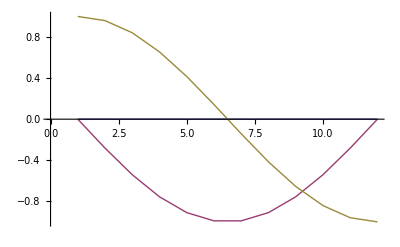

```mathematica
ρ0={{1,0},{0,0}};
data=EvalPulse[X/2,π,InitialState->ρ0,PollingInterval->0.3,Observables->{X,Y,Z}]
Observables[data]
ListPlot[Observables[data],Joined->True]
```

Observables has an option TimeVector which you can set to true to include time coordinates along with the observables:

{{{0,0},{π/11,0.},{(2 π)/11,0.},{(3 π)/11,0.},{(4 π)/11,0.},{(5 π)/11,0.},{(6 π)/11,0.},{(7 π)/11,0.},{(8 π)/11,0.},{(9 π)/11,0.},{(10 π)/11,0.},{π,0.}},{{0,0},{π/11,-0.281733},{(2 π)/11,-0.540641},{(3 π)/11,-0.75575},{(4 π)/11,-0.909632},{(5 π)/11,-0.989821},{(6 π)/11,-0.989821},{(7 π)/11,-0.909632},{(8 π)/11,-0.75575},{(9 π)/11,-0.540641},{(10 π)/11,-0.281733},{π,-1.66533×10^-16}},{{0,1},{π/11,0.959493},{(2 π)/11,0.841254},{(3 π)/11,0.654861},{(4 π)/11,0.415415},{(5 π)/11,0.142315},{(6 π)/11,-0.142315},{(7 π)/11,-0.415415},{(8 π)/11,-0.654861},{(9 π)/11,-0.841254},{(10 π)/11,-0.959493},{π,-1.}}}

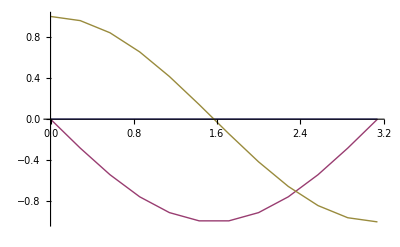

```mathematica
ρ0={{1,0},{0,0}};
data=EvalPulse[X/2,π,InitialState->ρ0,PollingInterval->0.3,Observables->{X,Y,Z}];
Observables[data,TimeVector->True]
ListPlot[Observables[data,TimeVector->True],Joined->True]
```

Observables[data,n] extracts only the data from the n’th observable:

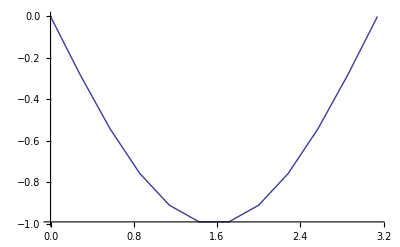

```mathematica
ρ0={{1,0},{0,0}};
ListPlot[Observables[EvalPulse[X/2,π,InitialState->ρ0,PollingInterval->0.3,Observables->{X,Y,Z}],2,TimeVector->True],Joined->True]
```

#### Functions

Functions[data] and Functions[data,n] behave identically to Observables; see the previous subsection.

### Time Dependence

#### First Example

The Hamiltonian H can be either time dependent, in which case it is just a matrix, or time dependent, in which case it is a function taking one real argument, and returning a matrix. In the previous sections we saw many time dependent examples. Here is a time dependent example with a DriftPulse:

{{Observables,{{1},{0.99995},{0.9998},{0.99955},{0.999201},{0.998751},{0.998202},{0.997553},{0.996804},{0.995956},{0.995008},{0.993961},{0.992815},{0.991569},{0.990224},{0.98878},{0.987238},{0.985597},{0.983857},{0.982019},{0.980083},{0.978049},{0.975917},{0.973688},{0.971362},{0.968938},{0.966418},{0.963801},{0.961088},{0.958278},{0.955373},{0.952373},{0.949277},{0.946087},{0.942802},{0.939423},{0.93595},{0.932383},{0.928723},{0.924971},{0.921126},{0.917189},{0.91316},{0.90904},{0.90483},{0.900529},{0.896138},{0.891657},{0.887087},{0.882429},{0.877682},{0.877682}}},{TimeVector,{0,1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10,1,11/10,6/5,13/10,7/5,3/2,8/5,17/10,9/5,19/10,2,21/10,11/5,23/10,12/5,5/2,13/5,27/10,14/5,29/10,3,31/10,16/5,33/10,17/5,7/2,18/5,37/10,19/5,39/10,4,41/10,21/5,43/10,22/5,9/2,23/5,47/10,24/5,49/10,5,5}}}

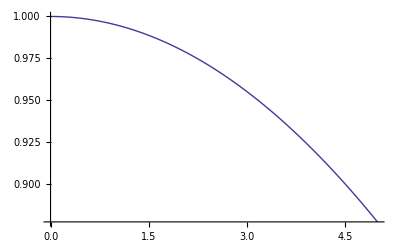

```mathematica
H[t_]=Sin[t]X;
data=EvalPulse[H,5,PollingInterval->0.1,InitialState->Projector[{1,0}],Observables->{Z}]
ListPlot[Observables[data,TimeVector->True],Joined->True]
```

#### Controlling the StepSize

NVSim simulates time dependence by discretizing the time domain and assuming the Hamiltonian is constantly equal to the Hamiltonian at the midpoint on each of these small intervals. If no StepSize is given, one is automatically calculated by taking a tenth of the inverse of the norm of the Hamiltonian, minimized over all time. This may work, but in some cases this fails (eg your Hamiltonian is unbounded over time, eg H=t^2 X), and in some cases a value that is too small or too large is chosen. In these latter cases you will want to choose the value yourself:

{{Observables,{{1},{0.99995},{0.9998},{0.999551},{0.999201},{0.998752},{0.998204},{0.997555},{0.996807},{0.995959},{0.995012},{0.993966},{0.992821},{0.991576},{0.990232},{0.98879},{0.987248},{0.985609},{0.98387},{0.982034},{0.980099},{0.978067},{0.975937},{0.97371},{0.971385},{0.968964},{0.966445},{0.963831},{0.96112},{0.958313},{0.95541},{0.952412},{0.949319},{0.946131},{0.942849},{0.939472},{0.936002},{0.932438},{0.928781},{0.925032},{0.92119},{0.917256},{0.913231},{0.909114},{0.904907},{0.900609},{0.896222},{0.891745},{0.887179},{0.882524},{0.877781},{0.877781}}},{TimeVector,{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.,5}}}

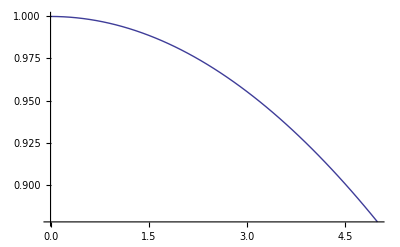

```mathematica
H[t_]=Sin[t]X;
data=EvalPulse[H,5,PollingInterval->0.1,InitialState->Projector[{1,0}],Observables->{Z},StepSize->0.01]
ListPlot[Observables[data,TimeVector->True],Joined->True]
```

You can check the value that would be chosen automatically with GetStepSize:

```mathematica
H[t_]=Sin[t]X;
GetStepSize[H]
```

1/10

To be clear: the StepSize and the PollingInterval are completely different and unrelated numbers. As an illustration, increasing the StepSize will decrease the accuracy of the simulation, whereas increasing the PollingInterval will simply course grain your plots.

### Shaped Pulses

The pulse shape can be specified either in a Mathematica matrix, or as a path to an external text file.

#### Example with matrix

In this example we use two control Hamiltonians, and only a handful of steps. The first element in each row of the shape matrix is the time of that step, and the rest are the amplitudes of the same step.

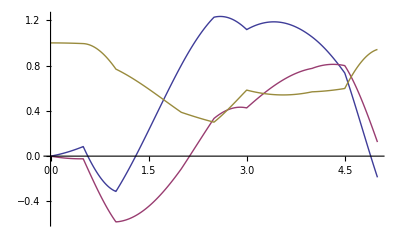

```mathematica
shape={{0.5,.1,.2},{0.5,1.4,0},{1.,.3,.4},{0.5,.1,.2},{0.5,1.4,0},{1.,.3,.4},{0.5,.1,.2},{0.5,1.4,0}};
Hctl1=X/2;
Hctl2=Y/2;
data=EvalPulse[
Z/2,
{shape,{Hctl1,Hctl2}},
StepSize->10^-2,
PollingInterval->0.01,
InitialState->Projector[{1,0}],
Observables->{X+Y,Y,Z}
];
ListPlot[Observables[data,TimeVector->True],Joined->True]
```

#### Example with file

Every line of the file should be separated by some delimeter (comma, tab, I’m not sure what else woud work). The first column contains the time steps, the second to last column contain the amplitudes. Mathematica is pretty clever when importing files, so you can use scientific notation (0.5e-9) and stuff.

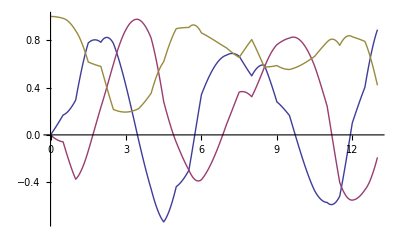

```mathematica
SetDirectory[NotebookDirectory[]];
Hctl1=X/2;
Hctl2=Y/2;
data=EvalPulse[
Z/2,
{"shape.csv",{Hctl1,Hctl2}},
PollingInterval->.05,
InitialState->Projector[{1,0}],
Observables->{X,Y,Z}
];
ListPlot[Observables[data,TimeVector->True],Joined->True]
```

You can import the file to the matrix form as used in the previous subsection with GetPulseShapeMatrix:

```mathematica
SetDirectory[NotebookDirectory[]];
GetPulseShapeMatrix["shape.csv"]
```

{{0.5,0.2,0.3},{0.5,0.9,0.03},{0.5,0.1,0.9},{0.5,0.1,0.1},{0.5,0.2,1.},{1.,0.1,0.2},{0.5,0.2,0.3},{0.5,0.9,0.03},{0.5,0.1,0.9},{0.5,0.1,0.1},{0.5,0.2,1.},{1.,0.1,0.2},{0.5,0.2,0.3},{0.5,0.9,0.03},{0.5,0.1,0.9},{0.5,0.1,0.1},{0.5,0.2,1.},{1.,0.1,0.2},{0.5,0.2,0.3},{0.5,0.9,0.03},{0.5,0.1,0.9},{0.5,0.1,0.1},{0.5,0.2,1.}}

### Pulse Sequences

Pulse sequences can be simulated using the EvalPulseSequence[H,{p1,p2,p3,...}] function. This function does little more than evaluate EvalPulse[H,p1], EvalPulse[H,p2], etc. back to back. The “little more” it does do is very convenient: it ties the end result of the previous pulse into the initial conditions of the current pulse. For example, on the first pulse it will take InitialState as the initial state, but on subsequent pulses it will take the end state of the previous pulse as the initial state.

#### Example

Let’s just perform some random collection of pulses.

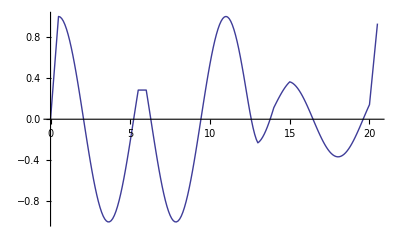

```mathematica
p1={(X+Z)/Sqrt[2],0.5};
p2=5;
p3={X,0.5};
p4=5;
p5={{{1,.1,.2},{1,1.4,0},{1.,.3,.4},{1,.1,.2}},{X/2,Y/2}};
p6=5;
p7=p1;
data=EvalPulseSequence[Z/2,{p1,p2,p3,p4,p5,p6,p7},InitialState->Projector[{1,0}],Observables->{X},PollingInterval->0.1];
ListPlot[Observables[data,TimeVector->True],Joined->True]
```

#### Symbolic Example

Here we sandwich a DriftPulse of length t by two Haadamards on the first qubit.

```mathematica
H=BlockMatrix[ϵ Z,δ X];
U=HadamardMatrix[2]⊗𝟙;
H//MatrixForm
$Assumptions=t>0&&ϵ>0&&δ>0;
data=EvalPulseSequence[H,{{U,1},t,{U,1}},InitialState->Projector[{1,0}]⊗𝟙/2];
MatrixForm@Simplify@PartialTr[ExpToTrig@Last@States@data,{2,2},{2}]
```

(ϵ | 0 | 0 | 0
0 | -ϵ | 0 | 0
0 | 0 | 0 | δ
0 | 0 | δ | 0)

(1/2 (1+Cos[t δ] Cos[t ϵ]) | 0
0 | 1/2 (1-Cos[t δ] Cos[t ϵ]))

#### Drawing pulse sequences

This feature still needs some work, but, for example:

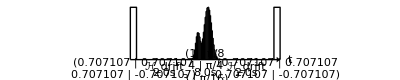

```mathematica
shapedpulse={{{1,π/8},{4,π/4},{3,π/16}},{X/2}};
seq={{(X+Z)/Sqrt[2],.1},2,shapedpulse,2,{(X+Z)/Sqrt[2],.1}};
DrawSequence[seq]
```

### Tips, Tricks and Troubleshooting

#### EvalPulse/EvalPulseSequence not evaluating

Sometimes something won’t evaluate at all:

```mathematica
p1={(X+Z)/Sqrt[2],0.5};
p2=5;
p3=X;
p4=5;
p5={{{1,.1,.2},{1,1.4,0},{1.,.3,.4},{1,.1,.2}},{X/2,Y/2}};
p6=5;
p7=p1;
EvalPulseSequence[Z/2,{p1,p2,p3,p4,p5,p6,p7},InitialState->Projector[{1,0}],Observables->{X},PollingInterval->0.1]
```

EvalPulseSequence[{{1/2,0},{0,-1/2}},{{{{1/(√2),1/(√2)},{1/(√2),-1/(√2)}},0.5},5,{{0,1},{1,0}},5,{{{1,0.1,0.2},{1,1.4,0},{1.,0.3,0.4},{1,0.1,0.2}},{{{0,1/2},{1/2,0}},{{0,-ⅈ/2},{ⅈ/2,0}}}},5,{{{1/(√2),1/(√2)},{1/(√2),-1/(√2)}},0.5}},InitialState→{{1,0},{0,0}},Observables→{{{0,1},{1,0}}},PollingInterval→0.1]

This is often caused by inputs in the wrong format. You can use PulseQ to test which of the pulses are valid:

```mathematica
PulseQ/@{p1,p2,p3,p4,p5,p6,p7}
```

{True,True,False,True,True,True,True}

We see that we forgot to include the time of the instantaneous pulse p3.

#### Simulating ranges of parameters

Simulating ranges of parameters is not builtin, but you can get around this with not too much effort. Suppose we want to simulate a Ramsey experiment (π/2 - τ - π/2: now vary τ and take the FT).

```mathematica
rot={MatrixExp[-I π/4(Sx+Sxp)/Sqrt[2]]⊗𝟙//N,1 10^-8};
Ham[t_]=Simplify[With[{Hint= 10^-6 NVHamiltonian[]⊗𝟙},MatrixExp[I t Hint].(10^-6 NVHamiltonian["nitrogenIsotope"->14,"B"->{10,0,0}]-Hint).MatrixExp[-I t Hint]]];
ρ0=Projector[{0,1,0}]⊗𝟙/3;
```

Warning: this will take like 20 minutes to run.

```mathematica
data=Table[
{
τ,
Last@Last@Observables@EvalPulseSequence[
Ham,
{rot,τ,rot},
StepSize->0.3 10^-3,
InitialState->ρ0,
Observables->{Projector[{0,1,0}]⊗𝟙}
]
},
{τ,.01,10,.01}
];
```

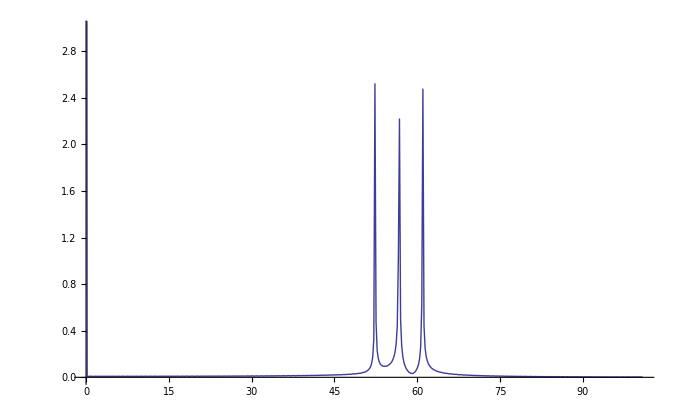

```mathematica
DiscreteFourierPlot[data[[All,2]],{0.05,5},{Abs},Joined->True,PlotRange->{0,3}]
```